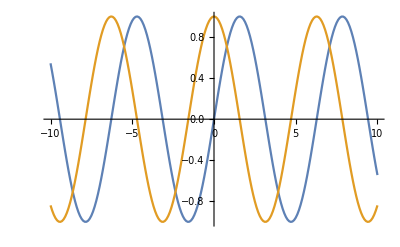

```mathematica
s1[x_]:=Sin[x];
s2[x_]:=Cos[x];
r:=Range[-10,10,.1];
s1p:=Map[s1,r];
s2p:=Map[s2,r];
ListLinePlot[{s1p,s2p},DataRange->{-10,10}]
```

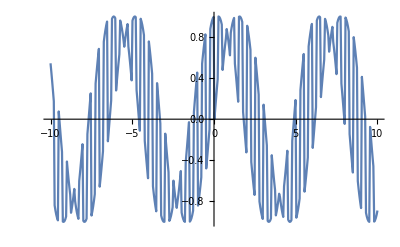

```mathematica
res:=List[];
For[i=1,i<Length[s1p],i+=5,
res=Join[res,s1p[[Range[i,i+4]]]];
res=Join[res,s2p[[Range[i,i+4]]]];
]
ListLinePlot[res,DataRange->{-10,10}]
```

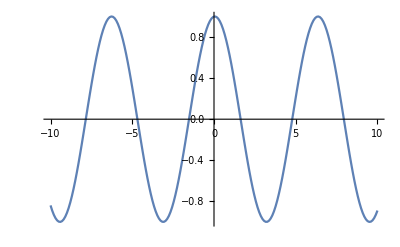

```mathematica
nres=List[];
For[i=1+5,i<Length[res],i+=10,
nres=Join[nres,res[[i;;i+4]]]
]
ListLinePlot[nres,DataRange->{-10,10}]
```